```mathematica
SetOptions[ListPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Times",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
dir1="2018-12-18-17-09-34";
SetDirectory["D:\\VELA\\GIT Projects\\Software\\Apps\\RF_Conditioner\\logs\\HRRG\\"<>dir1];
fn=Select[FileNames[],StringTake[#,{-3,-1}]=="wxf"&]
data=Import[fn⟦1⟧];
Keys[data]
```

```mathematica
traceKeyHeads={"value_HRRG_CAVITY_FORWARD_PHASE","value_HRRG_CAVITY_FORWARD_POWER","value_HRRG_CAVITY_PROBE_PHASE","value_HRRG_CAVITY_PROBE_POWER","value_HRRG_CAVITY_REVERSE_PHASE","value_HRRG_CAVITY_REVERSE_POWER"}
tracesuffix={"_-2","_-1","_0","_1","_1"}
```

{value_HRRG_CAVITY_FORWARD_PHASE,value_HRRG_CAVITY_FORWARD_POWER,value_HRRG_CAVITY_PROBE_PHASE,value_HRRG_CAVITY_PROBE_POWER,value_HRRG_CAVITY_REVERSE_PHASE,value_HRRG_CAVITY_REVERSE_POWER}

{_-2,_-1,_0,_1,_1}

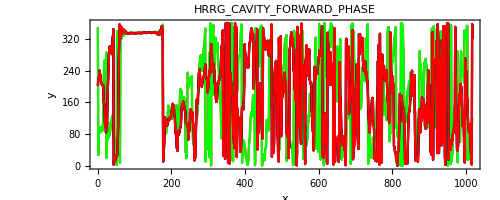
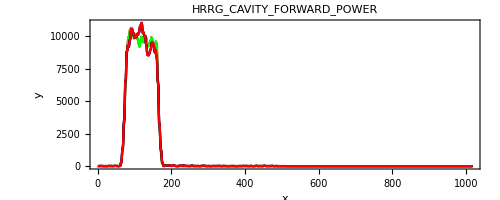
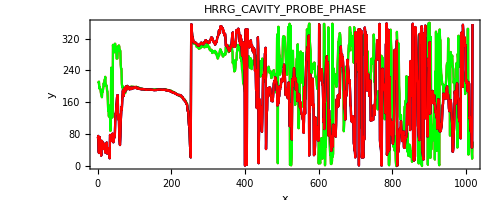
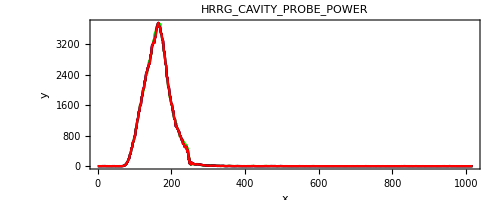
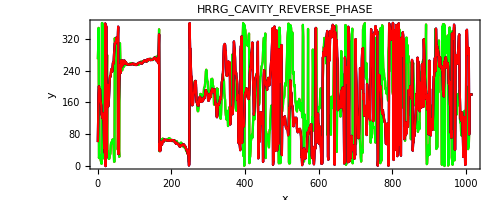
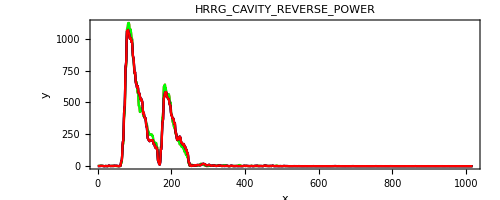

```mathematica
Table[
ListPlot[Lookup[data,traceKeyHeads⟦i⟧<>#&/@tracesuffix]⟦1⟧,PlotLabel->StringTake[traceKeyHeads⟦i⟧,{7,-1}]]
,{i,1,Length@traceKeyHeads}]
```